Student ID = { # } | Total Mark = mark | Marker =

## Instructions

Time allowed : 3 hours

ENTER YOUR STUDENT NUMBER IN THE BOX ABOVE

Save your notebook now and save regularly during the test in case your computer crashes.

This is an “open-book” exam. You are permitted to bring in printed or electronic copies of your lecture notes and assignment solutions, and to access electronic resources such as the Documentation Center and the internet. You can use your own laptop if you prefer.

Spoken or electronic communication via email, messaging, chat, file transfer, etc. is not permitted. This includes Facebook and collaborative work via a Wiki. Such action may result in your being deprived of any credit for this examination or even, in some cases, for the whole unit. This will apply regardless of whether the material has been used at the time it is found.

Insert your solutions—both Mathematica code and text— into cells immediately following the part of the question that you are answering.

Do not upload your solutions using the Upload button above until asked to do so by the examination supervisor.

Stay seated and do not talk until the examination supervisor verifies that all notebooks have been uploaded.

## Graphics

Elliptic curve [2 Marks]

Use Manipulate and ContourPlot to visualize the elliptic curve y^2==x^3+a x+b over [-3,3]×[-3,3] as a function of the parameters a and b for -3≤a≤3 and -3≤b≤3. [2 Marks]

Solution

## Programming

Iteration [5 Marks]

Given the vertices of an triangle in the plane,

```mathematica
vertices=N[({{0, 0}, {1, 0}, {0.3, 1}})];
```

displayed using Polygon,

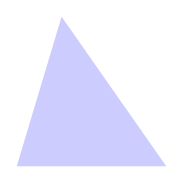

```mathematica
triangle=Graphics[{Blue,Opacity[0.2],Polygon[vertices]},PlotRange->{{0,1},{0,1}},AspectRatio->Automatic]
```

and an arbitrary starting point:

```mathematica
start=RandomReal[{0,1},{2}]
```

{0.498282,0.326802}

consider the following iterative scheme:

At each step, define a function called next[point_]:=... which selects one of the vertices at random (using RandomChoice), and computes the next point in the iterative sequence by taking the midpoint between the current point, point, and the selected vertex. [2 Marks]

Iterate this operation 5 10^4 times from start using NestList. [1 Mark]

Display the sequence of points overlaid onto triangle, using Take and Manipulate to control how many points are displayed. [2 Marks]

Solution

## Linear Algebra

Conic sections [5 Marks]

Conic sections have the form of a second-degree polynomial:

a x^2+b x y+c y^2+d x+e y+f==0

A curve passing through five points {x_i,y_i}_(i=1,…5) can be computed by solving the following determinantal equation:

|x^2 | x y | y^2 | x | y | 1
x_1^2 | x_1 y_1 | y_1^2 | x_1 | y_1 | 1
x_2^2 | x_2 y_2 | y_2^2 | x_2 | y_2 | 1
x_3^2 | x_3 y_3 | y_3^2 | x_3 | y_3 | 1
x_4^2 | x_4 y_4 | y_4^2 | x_4 | y_4 | 1
x_5^2 | x_5 y_5 | y_5^2 | x_5 | y_5 | 1|==0

Use the determinantal equation (DisplayFormulaNumbered) to compute the equation of the curve passing through 5 randomly chosen points, computed using RandomReal. [3 Marks]

Use ContourPlot to visualize the curve. Show the curve together with the points. [2 Marks]

Solution

Hermitian matrices [7 Marks]

Consider the general 3×3 Hermitian traceless matrix

```mathematica
ℋ=({{α, β+ⅈ γ, δ+ⅈ ϵ}, {β-ⅈ γ, ϕ, η+ⅈ κ}, {δ-ⅈ ϵ, η-ⅈ κ, -α-ϕ}});
```

where all the parameters α,β,…,κ are real.

How many parameters are there in this matrix? [1 Mark]

Verify that ℋ is Hermitian and has zero trace (Hint: use ConjugateTranspose, ComplexExpand, and Tr). [2 Marks]

Show that the set of matrices

```mathematica
X/:Subscript[X, 1]=({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});X/:Subscript[X, 2]=({{0, -ⅈ, 0}, {ⅈ, 0, 0}, {0, 0, 0}});X/:Subscript[X, 3]=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});X/:Subscript[X, 4]=({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});X/:Subscript[X, 5]=({{0, 0, -ⅈ}, {0, 0, 0}, {ⅈ, 0, 0}});X/:Subscript[X, 6]=({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});X/:Subscript[X, 7]=({{0, 0, 0}, {0, 0, -ⅈ}, {0, ⅈ, 0}});X/:Subscript[X, 8]=({{1, 0, 0}, {0, 1, 0}, {0, 0, -2}});
```

form a basis for 3×3 Hermitian traceless matrices (Hint: this means that ℋ can be written as a linear combination of the Χ_i). [2 Marks]

The commutator of two matrices (or operators) is denoted

[A,B]==A.B-B.A

Show that each commutator [X_a,X_b] can be expressed as a linear combination of X_c. [2 Marks]

Solution

## Calculus

Nonlinear differential equation [3 Marks]

Consider the nonlinear differential equation

w''(z)==2(w(z))^3+z w(z)

with initial conditions

w(0)==a
w'(0)==b

Use NDSolve to compute numerical solutions to (DisplayFormulaNumbered) over -10≤z≤3. [1 Mark]

Use Manipulate to plot w(z) as a function of a and b for 0≤a≤0.5 and -0.2≤b≤0 and compare with 1/2 z. [2 Marks]

Solution

Functional equation [3 Marks]

Consider the functional equation

f(z)=α f(f(z /α)).

One method for computing the value of α for which f(z) exists is to assume that

f_n(z)=1+∑_(k=1)^n c_k z^(2k),

and compute successive approximations to α for n=1,2,3,…, using series expansion of (both sides) of equation (DisplayFormulaNumbered).

Use series expansion and Solve to compute approximate values of α<0 and c_1<0 for n=1. These approximate values can be obtained exactly. [2 Marks]

Use series expansion and NSolve to compute approximate values of α<0, c_1<0, and c_2 for n=2. [1 Mark]

Solution

## Variational Methods

Coulomb potential inside heavy neutral atoms [7 Marks]

The nonlinear differential equation

ϕ''(x)==(ϕ(x))^(3/2)/(√x),

along with the boundary conditions

ϕ(0)==1,ϕ(∞)==0,

describes the screening of the Coulomb potential inside heavy neutral atoms. However, there is no closed-form solution of equation (DisplayFormulaNumbered).

The Euler–Lagrange equation

(∂ℱ)/(∂ϕ)-ⅆ_x(∂ℱ)/(∂ϕ')==0

applied to the functional

ℱ[ϕ][x]==1/2(ϕ'(x))^2+2/5(ϕ(x))^(5/2)/(√x)

yields the differential equation (DisplayFormulaNumbered).

Show that ϕ_0(x)==144 x^-3 satisfies the differential equation (DisplayFormulaNumbered) for x≥0 and the second boundary condition ϕ(∞)==0. [2 Marks]

Show that the Euler–Lagrange equation (DisplayFormulaNumbered) applied to functional (DisplayFormulaNumbered) yields the differential equation (DisplayFormulaNumbered). [2 Marks]

Consider the two-parameter trial function

ϕ_(α,β)(x)=1/((1+(x/β)^(3/α))^α)

Given that

⟨ℱ_(α,β)⟩=∫_0^∞ ℱ[ϕ_(α,β)][x]==(4 √β α/6+1 (7 α)/3)/(5 (5 α)/2)+(9 2-α/3 (7 α)/3+1)/(14 β 2 α+2)

use FindRoot to obtain the optimal values of α>0 and β>0 by determining the stationary value of ⟨ℱ_(α,β)⟩, and plot the resulting variational solution ϕ_(α,β)(x). [3 Marks]

Solution

## Fourier Series

Fourier Transform [8 Marks]

The Fourier transform of a function f(t) is defined to be

f̃(ω)==1/(2π)∫_(-∞)^∞ f(t)ⅇ^(ⅈ ω t)ⅆt

The inverse Fourier transform of a function f̃(ω) is defined to be

f(t)==∫_(-∞)^∞ f̃(ω)ⅇ^(-ⅈ ω t)ⅆω

Consider the function

s(t)=Piecewise[{{1, -1<t<1}, {0, Abs[t]≥1}}]

Compute the Fourier transform s̃(ω) of s(t) and plot it for -12≤ω≤12. [2 Marks]

Compute the complex Fourier coefficients c_n of s(t) for t∈[-π,π], with s(t) periodically extended outside this interval. [2 Marks]

Use DiscretePlot to visualize c_n for -12≤n≤12. [1 Mark]

Verify that c_n==s̃(n). [1 Mark]

Compute the inverse Fourier transform of s̃(ω) and verify that you recover s(t). [2 Marks]

Solution

## Special Functions

Roots of the Airy function [9 Marks]

The Airy function Ai(z) can be written as an infinite product over its roots,

Ai(z)==Ai(0)ⅇ^(z 0/0)∏_(n=1)^∞ (1-z/a_n)ⅇ^(z/a_n)

where a_n is the n^th zero of Ai(z). The logarithmic derivative of Ai(z) reads

(Ai'(z))/(Ai(z))==0/0-∑_(k=1)^∞ z^k Z(k+1)

where

Z(k)==∑_(n=1)^∞ 1/a_n^k

Plot z over -15≤z≤5. What do you observe about the location and spacing of the roots of z? [2 Marks]

The zeros of the z are built-in as AiryAiZero. Use N to compute numerical values of the first 1000 roots. [1 Mark]

Compute Z(2), Z(3), and Z(4) exactly by computing the Maclaurin series expansion of equation (DisplayFormulaNumbered). [2 Marks]

Show that Z(2), Z(3), and Z(4) are polynomials in r=0/0. [2 Marks]

Compare Z(2), Z(3), and Z(4) with the numerical value of the truncated sum (DisplayFormulaNumbered), computed using the numerical roots. [2 Marks]

Solution

## Orthogonal Polynomials

Polynomials via determinants  [6 Marks]

Consider the matrices

A_n==(1 | x | ⋯ | x^n
m_1 | m_2 | ⋯ | m_(n+1)
⋮ | ⋮ | ⋱ | ⋮
m_n | m_(n+1) | ⋯ | m_(2n)), B_n==(m_0 | m_1 | ⋯ | m_n
m_1 | m_2 | ⋯ | m_(n+1)
⋮ | ⋮ | ⋱ | ⋮
m_n | m_(n+1) | ⋯ | m_(2n)),

where m_k is the k^th moment of x,

m_k=∫_0^∞ ⅇ^-x x^k ⅆx

The ratio of the determinants of these matrices,

ℒ_n(x)==Det[A_n]/Det[B_n]

generates a set of orthogonal polynomials with respect to the inner product

⟨f,g⟩=∫_0^∞ x ⅇ^-x f(x)g(x)ⅆx

Compute and save m_k. [1 Mark]

Use SparseArray to define the matrices A_n and B_n in equation (DisplayFormulaNumbered) for general n. [2 Marks]

Compute ℒ_n(x) using equation (DisplayFormulaNumbered) for n=0,1,…,5. [1 Mark]

Verify that this set of polynomials is orthogonal with respect to the inner product (DisplayFormulaNumbered). [2 Marks]

Solution